# 1-D Percolation

```mathematica
array=Module[{p=.6},Table[If[RandomReal[]<p,1,0],{i,100}]];
array
```

{1,0,1,1,1,1,1,1,0,0,1,1,0,1,0,1,0,0,1,1,1,1,1,1,0,1,1,0,1,0,1,0,0,1,1,1,1,1,1,0,0,0,0,1,1,1,1,0,0,1,0,1,1,0,1,1,1,1,0,0,0,1,0,0,1,1,0,0,1,1,1,0,0,1,1,0,0,0,0,0,1,1,1,1,1,1,1,1,1,0,1,1,0,1,0,1,1,0,1,1}

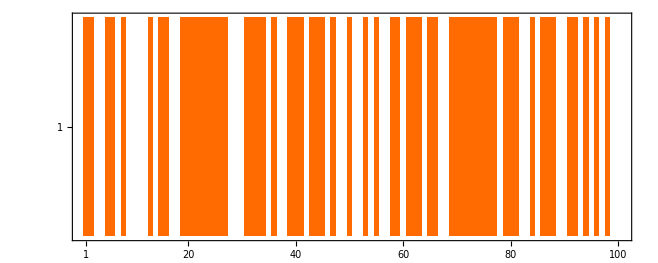

```mathematica
MatrixPlot[{array}]
```

```mathematica
counts[m_]:=#/.ComponentMeasurements[#,"Count"]&@MorphologicalComponents[m,CornerNeighbors->False]
```

```mathematica
counts[{array}]
```

{{2,2,0,5,5,5,5,5,0,1,0,2,2,0,0,1,0,1,0,1,0,0,1,0,0,2,2,0,1,0,1,0,2,2,0,0,1,0,0,0,1,0,0,0,0,0,1,0,0,0,0,1,0,0,1,0,6,6,6,6,6,6,0,3,3,3,0,0,2,2,0,0,1,0,2,2,0,1,0,0,0,0,2,2,0,0,0,3,3,3,0,1,0,1,0,0,3,3,3,0}}

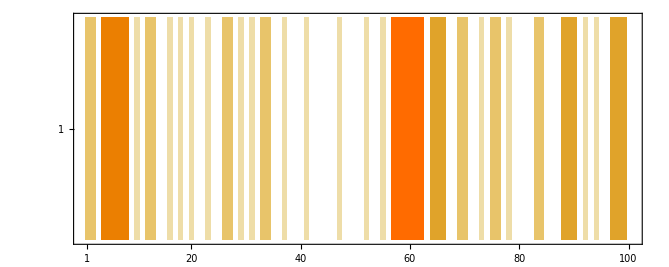

```mathematica
MatrixPlot[counts[{array}]]
```

```mathematica
NumberSitesPerClusterSize=Counts@(Join@@counts[{array}])
```

<|2→14,0→50,5→5,1→16,6→6,3→9|>

```mathematica
KeyValueMap[#1->#2/#1&,KeyDrop[NumberSitesPerClusterSize,0]]
```

{2→7,5→1,1→16,6→1,3→3}

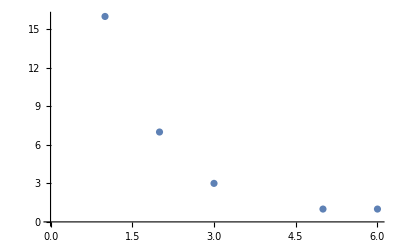

```mathematica
ListPlot[KeyValueMap[{#1,#2/#1}&,KeyDrop[NumberSitesPerClusterSize,0]]]
```

This depends on the size of the system!

```mathematica
Counts@(Join@@counts[{array}])
```

```mathematica
KeyValueMap[#1->#2/#1&,KeyDrop[Counts@(Join@@counts[{Module[{p=.6},Table[If[RandomReal[]<p,1,0],{i,249}]]}]),0]]//Sort
```

{1→18,2→23,3→8,4→7,6→1,7→2,8→1,9→1}

```mathematica
Attributes[MorphologicalComponents]
```

{Protected,ReadProtected}

```mathematica
Series[-1/(Log[1-x]),{x,0,2}]
```

1/x-1/2-x/12-x^2/24+O[x]^3

```mathematica
Series[(p+2)/p,{p,0,5}]
```

2/p+1+O[p]^6

```mathematica
D[1/Log[p],p-1]
```

General::ivar: -1+p is not a valid variable.

∂_(-1+p) 1/Log[p]

```mathematica
D[2/p+1,p]
```

-2/p^2

```mathematica
Series[1/x,{x,0,5}]
```

1/x+O[x]^6

```mathematica
{{},{a,a},{a,b},{a,a,a},{a}}/.{a}->x
```

{{},{a,a},{a,b},{a,a,a},x}

```mathematica
array
```

{1,0,1,1,1,1,1,1,0,0,1,1,0,1,0,1,0,0,1,1,1,1,1,1,0,1,1,0,1,0,1,0,0,1,1,1,1,1,1,0,0,0,0,1,1,1,1,0,0,1,0,1,1,0,1,1,1,1,0,0,0,1,0,0,1,1,0,0,1,1,1,0,0,1,1,0,0,0,0,0,1,1,1,1,1,1,1,1,1,0,1,1,0,1,0,1,1,0,1,1}

```mathematica
L=100000;p=.9;
```

```mathematica
array=Table[If[RandomReal[]<p,1,0],{i,L}];
NumberSitesPerClusterSize=Counts[Flatten[#/. {1->Length[#]}&/@Split[array]]]
ClusterSizeFrecuency=ResourceFunction["ToAssociations"][Flatten[KeyValueMap[{#1->#2/#1}&,KeyDrop[NumberSitesPerClusterSize,0]]]];
ClusterNumberDensity =ResourceFunction["ToAssociations"][Flatten[KeyValueMap[{#1->#2/#1}&,KeyDrop[NumberSitesPerClusterSize,0]/L]]];
```

<|1→880,0→9915,12→3024,21→2079,11→3256,7→3192,4→2612,9→3339,26→2262,17→2482,38→684,2→1604,10→3550,25→2050,5→2950,27→1647,6→3108,13→3237,29→1450,22→2596,14→3304,18→2448,8→3536,30→1440,40→600,3→2298,56→168,16→3040,20→2600,34→1292,53→212,19→2755,35→1050,41→615,28→1260,23→1955,15→2925,31→682,62→124,33→1056,24→1752,36→648,37→777,51→255,48→432,82→82,45→315,42→546,32→1312,50→200,46→322,55→330,61→244,43→516,67→67,39→351,57→228,70→140,47→235,44→176,54→162,101→202,52→104,63→252,83→83,49→245,60→120,66→66,59→59,68→68,69→69,58→58,65→65,73→73,80→80,89→89|>

```mathematica
ClusterSizeFrecuency[1]
```

933

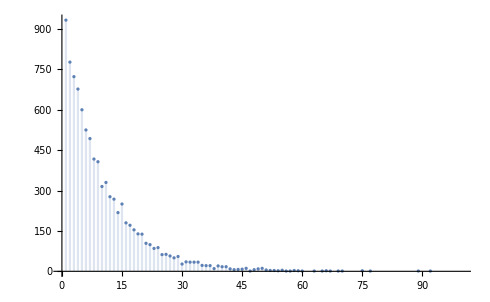

```mathematica
DiscretePlot[ClusterSizeFrecuency[x],{x,1,100}]
```

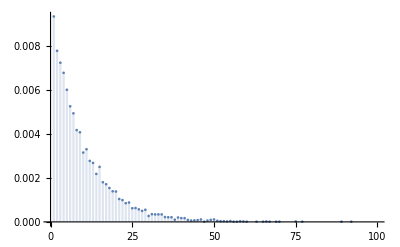

```mathematica
DiscretePlot[ClusterNumberDensity[x],{x,1,100}]
```

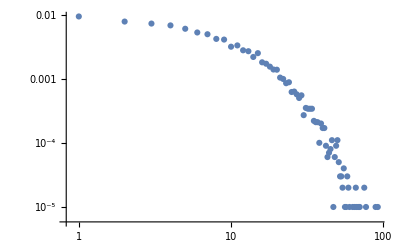

```mathematica
ListLogLogPlot[Table[{x,ClusterNumberDensity[x]},{x,1,1000}]]
```

```mathematica
ClusterSizeFrecuency
```

{{1→324},{18→7},{2→281},{7→70},{6→97},{4→163},{3→209},{20→10},{5→118},{12→32},{17→13},{9→49},{14→16},{15→18},{11→40},{10→47},{13→16},{8→67},{27→2},{16→14},{24→1},{21→8},{25→1},{28→1},{23→2},{26→2},{19→1},{22→1}}

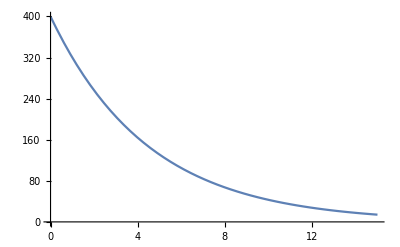

```mathematica
Plot[10000(1-p)^2p^s,{s,0,15}]
```

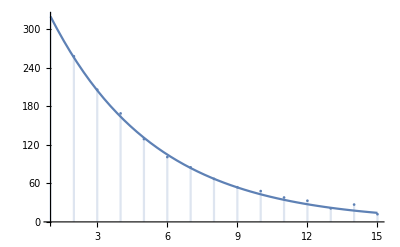

```mathematica
Show[Plot[10000(1-p)^2p^s,{s,1,15}],DiscretePlot[ClusterSizeFrecuency[x],{x,1,100}]]
```